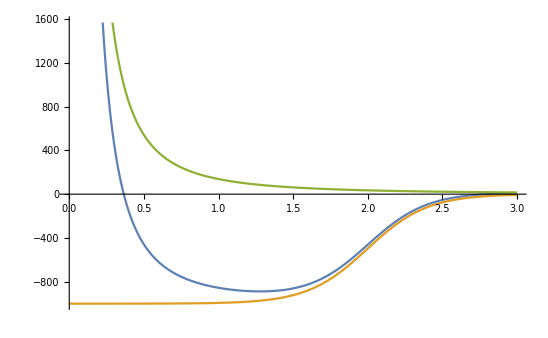

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=1000;R=2;a=0.2;μ=8/9 Subscript[m, N];l=2;
rmax=3;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{0,rmax}]
```

## BOUND SOLS

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k1[En_]:=Sqrt[-(2μ En)/ℏc^2];
B1[En_]:=1-dr k1[En];
H1new[En_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(-2+B1[En]);H)
eigenv1[{En_,i_}]:=({eval,evec}=Eigensystem[H1new[En]];{eval[[-i]],i})
```

```mathematica
n=4;
En=NestWhileList[eigenv1,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>0.00000001&,2,10][[-1,1]]
```

-508.343

```mathematica
{eval1,evec1}={eval,evec}[[All,Position[{eval,evec}[[1,All]],_?(#<0&)][[All,1]]]];
```

```mathematica
n
```

```mathematica
(*En=NestWhileList[SetPrecision[eigenv,5]{-V0,1},UnsameQ,2,100]*)
(*FindRoot[eigenv[{x,1}][[1]]==x,{x,-V0/2,-V0,0},WorkingPrecision->2]*)
(*Plot[{eigenv[{x,n}][[1]],#&[x]},{x,-V0,0}]*)
```

```mathematica
wave1[En_,r_]:=Exp[-k1[En] r];
const1[i_]:=evec1[[i,-1]]/wave1[eval1[[i]],rmax];
```

```mathematica
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,evec1⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],const1[i] wave1[eval1[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All],{i,1,Length[eval1],1}]
```

## SCATTERING SOLS

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
k2[En_]:=Sqrt[(2μ En)/ℏc^2];
B2[En_,δ_]:=1+dr Cot[k2[En] rmax+δ] k2[En];
H2new[En_,δ_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(-2+B2[En,δ]);H)

eigenv2[{En_,i_,δ_}]:=({eval,evec}=Eigensystem[H2new[En,δ]];{eval[[-i]],δ})
```

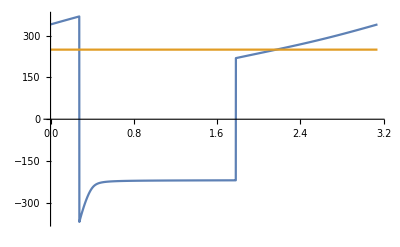

```mathematica
En=250.;
n=3;
(*phase=Table[{eigenv[{En,1,x}][[1]],x},{x,0,Pi,0.01}];*)
(*Solve[eigenv[{En,1,x}]==En,x]*)
(*FindRoot[eigenv[{En,1,δ}][[1]]==En,{δ,0,0,Pi},WorkingPrecision->2]*)
Plot[{eigenv2[{En,n,δ}][[1]],#&[En]},{δ,0,Pi},PlotRange->All]
```

```mathematica
phase=Table[{eigenv2[{En,n,δ}][[1]],δ},{δ,2.1,2.3,0.001}];
```

```mathematica
δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]]
```

2.168

```mathematica
{eval2,evec2}=Eigensystem[H2new[En,δ]];
```

```mathematica
wave2[En_,r_,δ_]:=Sin[k2[En] r+δ]
const2[i_]:=evec2[[-i,-1]]/wave2[eval2[[-i]],rmax,δ]
```

```mathematica
rmaxx=10;
Manipulate[ListLinePlot[{Transpose[{rlist,evec2⟦-i⟧}],Transpose[{Range[rmax,rmaxx,dr],const2[i] wave2[eval2[[-i]],Range[rmax,rmaxx,dr],δ]}]},PlotRange->All],{i,1,len,1}]
```